Define variable:

```mathematica
Needs["PhysicalConstants`"]
Subscript[E, 0]=1.602176487*^-19
m = 0.069*9.10938215*^-31
ℏ = 1.054571628251774*^-34
π = 3.14
T =300
Subscript[k, B]= 1.3806504*^-23
```

1.60218×10^-19

6.28547×10^-32

1.05457×10^-34

Set::wrsym: Symbol π is Protected.

3.14

300

1.38065×10^-23

General Expression:

```mathematica
n3=∫_(-∞)^0 1/(2*π^2)(√(2m/ℏ^2))^3*√-x/(1+Exp[(ef-x)/(Subscript[k, B] T)])ⅆx
```

-4.54827×10^23 PolyLog[3/2,-ⅇ^(-2.41432×10^20 ef)]

Non-degenerate case:

```mathematica
n1=∫_(-∞)^0 1/(2*π^2)(√(2m/ℏ^2))^3*√-x(Exp[(x-ef)/(Subscript[k, B] T)])ⅆx
```

4.54827×10^23 ⅇ^(-2.41432×10^20 ef)

Degenerate case:

```mathematica
n2 = ∫_ef^0 1/(2*π^2)(√(2m/ℏ^2))^3*√-x ⅆx
```

1.28352×10^54 (-ef)^(3/2)

Plot the figure:

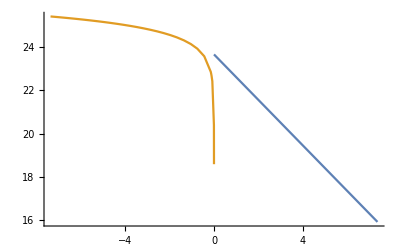

```mathematica
Plot[{ConditionalExpression[Log[10,n1],0≤ef<0.46*1.602176487*^-19],ConditionalExpression[Log[10,n2],-0.46*1.602176487*^-19<ef≤0]},{ef,-0.46*1.602176487*^-19,0.46*1.602176487*^-19},BaseStyle->Thickness[.02]]
```

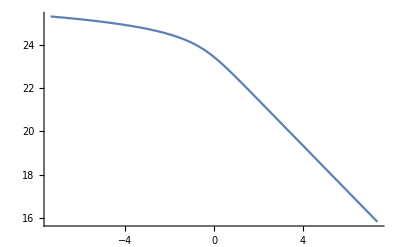

```mathematica
Plot[Log[10,n3],{ef,-0.82*1.602176487*^-19,0.82*1.602176487*^-19},BaseStyle->Thickness[.02]]
```

```mathematica
-4.548272002879405*^23 PolyLog[3/2,-ⅇ^(-2.4143210571867672*^20 *(0.09*1.602176487*^-19))]
```

1.38434×10^22

```mathematica
-3.5052159836277406*^23 PolyLog[3/2,-ⅇ^(-2.4143210571867672*^20 *(0.09*1.602176487*^-19))]
```

1.06687×10^22